```mathematica
SetDirectory[NotebookDirectory[]];
```

9.49701

10.2486

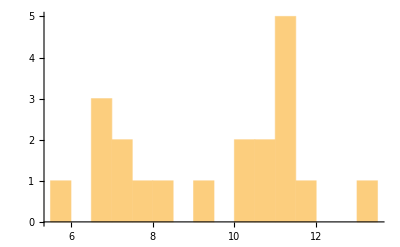

```mathematica
data=RandomVariate[NormalDistribution[10,2],{20}];
Mean@data
Median@data
Histogram[data,20]
```

```mathematica
Export["data_Posterior_PS_tumour.csv",data]
```

data_Posterior_PS_tumour.csv

```mathematica
HistogramList[data,20]
```

{{11/2,6,13/2,7,15/2,8,17/2,9,19/2,10,21/2,11,23/2,12,25/2,13,27/2},{1,0,3,2,1,1,0,1,0,2,2,5,1,0,0,1}}